```mathematica
data={{11,231},{13,328},{15,380},{17,459},{20,482},{24,497},{30,515},{40,530},{50,542}};
```

```mathematica
NonlinearModelFit[data,A*ut*v/0.030^2(1-Exp[-0.030^2/(ut*v)]),{{ut,0.01*10^-3},{A,550}},v]
```

FittedModel[33.0237 (1-ⅇ^(-21.4748/v)) v]

```mathematica
|
```

```mathematica
Dat[v_]:=33.023740805676034 (1-ⅇ^(-21.47478641534376/v)) v
```

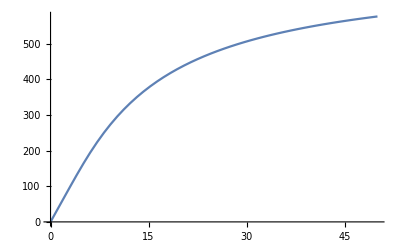

```mathematica
a1=Plot[Dat[v],{v,0,50}]
```

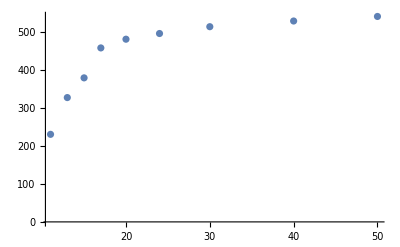

```mathematica
a2=ListPlot[data]
```

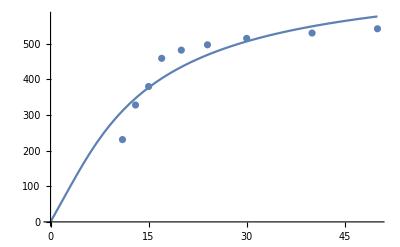

```mathematica
Show[a1,a2]
```